```mathematica
1. Первичная обработка данных.
```

### Ввод

```mathematica
data = Import[FileNameJoin[{NotebookDirectory[],"wineQualityReds.csv"}],"Data"];
Short[data,3](*Отобразим короткий вывод данных, чтобы посмотреть на переменные*)
data = data[[All,2;;-1]] ; 
data[[1]]
(*удалим столбцы с номарми объектов, они не понадобятся*)
```

{{id,fixed.acidity,volatile.acidity,citric.acid,residual.sugar,chlorides,free.sulfur.dioxide,total.sulfur.dioxide,density,pH,sulphates,alcohol,quality},{1,7.4,0.7,0,1.9,0.076,11,34,0.9978,3.51,0.56,9.4,5},{2,7.8,0.88,0,2.6,0.098,25,67,0.9968,3.2,0.68,9.8,5},{3,7.8,0.76,0.04,2.3,0.092,15,54,0.997,3.26,0.65,9.8,5},{4,11.2,0.28,0.56,1.9,0.075,17,60,0.998,3.16,0.58,9.8,6},«1590»,{1595,6.2,0.6,0.08,2,0.09,32,44,0.9949,3.45,0.58,10.5,5},{1596,5.9,0.55,0.1,2.2,0.062,39,51,0.99512,3.52,0.76,11.2,6},{1597,6.3,0.51,0.13,2.3,0.076,29,40,0.99574,3.42,0.75,11,6},{1598,5.9,0.645,0.12,2,0.075,32,44,0.99547,3.57,0.71,10.2,5},{1599,6,0.31,0.47,3.6,0.067,18,42,0.99549,3.39,0.66,11,6}}

{fixed.acidity,volatile.acidity,citric.acid,residual.sugar,chlorides,free.sulfur.dioxide,total.sulfur.dioxide,density,pH,sulphates,alcohol,quality}

```mathematica
1.1Описательная статистика
```

1.1 статистика Описательная

### Исходные данные содержат определенные признаки сортов вин. Для каждого из вин определено его качество, что является целевой переменной. Описание признаков, их типы и шкалы: fixed.acidity -> Содержание нелетучих кислот;

```mathematica
data[[All,1]];
%//Max
%%//Min
```

Max[15.9,fixed.acidity]

Min[4.6,fixed.acidity]

Признак принимает действительные значения и лежит в промежутке от 4.6 до 15.9

```mathematica
volatile.acidity -> Количество уксусной кислоты в вине, которое при слишком высоком уровне может привести к неприятному вкусу уксуса;
```

```mathematica
data[[All,2]];
%//Max
%%//Min
```

Max[1.58,volatile.acidity]

Min[0.12,volatile.acidity]

Признак принимает действительные значения и лежит в промежутке от 0,12 до 1,58

```mathematica
citric.acid -> Содержание лимонной кислоты;
```

```mathematica
data[[All,3]];
%//Max
%%//Min
%%%//Short
```

Max[1,citric.acid]

Min[0,citric.acid]

{citric.acid,0,0,0.04,0.56,0,0,0.06,0,0.02,0.36,0.08,0.36,0,0.29,0.18,0.19,0.56,0.28,0.08,0.51,0.48,0.31,0.21,0.11,0.14,0.16,0.24,0.21,0,0,«1538»,0.13,0.14,0.53,0.14,0.32,0.2,0.78,0.4,0.63,0.15,0.15,0.09,0.33,0.09,0.1,0.29,0.44,0.44,0.41,0.11,0.33,0.2,0.15,0.09,0.13,0.08,0.08,0.1,0.13,0.12,0.47}

Признак принимает действительные значения и лежит в промежутке от 0 до 1

```mathematica
residual.sugar -> Содержание сахара, остающегося после прекращения брожения;
```

```mathematica
data[[All,4]];
%//Max
%%//Min
```

Max[15.5,residual.sugar]

Min[0.9,residual.sugar]

Признак принимает действительные значения и лежит в промежутке от 0,9 до 15.5

```mathematica
chlorides -> Количество солей в вине;
```

```mathematica
data[[All,5]];
%//Max
%%//Min
```

Max[0.611,chlorides]

Min[0.012,chlorides]

Признак принимает действительные значения и лежит в промежутке от 0.012 до 0.611

```mathematica
free.sulfur.dioxide->свободная форма SO2 существующая в равновесии между молекулярным SO2 (в виде растворенного газа) и бисульфит-ионом
количество свободных и связанных форм S02
```

free.sulfur.dioxide→-ионом+в^2 и виде газа между форма бисульфит свободная равновесии молекулярным существующая растворенного SO2^2

и форм свободных связанных количество S02

```mathematica
data[[All,6]];
%//Max
%%//Min
```

Max[72,free.sulfur.dioxide]

Min[1,free.sulfur.dioxide]

```mathematica
%%%//Short
```

{free.sulfur.dioxide,11,25,15,17,11,13,15,15,9,17,15,17,16,9,52,51,35,16,6,17,29,23,10,9,21,11,4,10,14,8,17,22,15,40,13,5,3,13,7,12,12,17,8,9,5,8,22,12,5,12,4,8,6,30,33,25,«1486»,29,14,12,16,17,12,19,17,17,18,32,18,15,15,12,15,66,31,31,31,12,12,12,26,24,12,25,15,19,15,35,15,23,12,16,13,13,24,9,24,13,32,24,22,34,18,34,29,26,16,29,28,32,39,29,32,18}

Признак принимает целые значения и лежит в промежутке от 1 до 72

```mathematica
total.sulfur.dioxide ->количество свободных и связанных форм S02
```

total.sulfur.dioxide→и форм свободных связанных количество S02

```mathematica
data[[All,7]];
%//Max
%%//Min
%%%//Short
```

Max[289,total.sulfur.dioxide]

Min[6,total.sulfur.dioxide]

{total.sulfur.dioxide,34,67,54,60,34,40,59,21,18,102,65,102,59,29,145,148,103,56,29,56,60,71,37,67,40,23,11,37,35,16,82,37,113,83,50,18,15,30,19,87,87,46,14,23,11,65,114,37,12,96,23,«1497»,50,24,26,27,54,28,23,24,20,23,115,131,131,131,20,20,20,42,52,20,42,34,35,25,104,50,92,20,29,27,20,32,26,32,27,98,34,48,60,28,102,79,35,26,40,38,44,51,40,44,42}

Признак принимает целые значения и лежит в промежутке от 6 до 289

```mathematica
density -> Плотность вина. Она близка к плотности воды в зависимости от процента содержания алкоголя и сахара
```

density→в и к от воды близка сахара алкоголя процента Плотность плотности содержания зависимости вина.Она

```mathematica
data[[All,8]];
%//Max
%%//Min
```

Max[1.00369,density]

Min[0.99007,density]

Признак принимает действительные значения и лежит в промежутке от 0,99 до 1,00369

```mathematica
pH -> Показывает кислотность вина
```

pH→вина Показывает кислотность

```mathematica
data[[All,9]];
%//Max
%%//Min
%%%//Short
```

Max[4.01,pH]

Min[2.74,pH]

{pH,3.51,3.2,3.26,3.16,3.51,3.51,3.3,3.39,3.36,3.35,3.28,3.35,3.58,3.26,3.16,3.17,3.3,3.11,3.38,3.04,3.39,3.52,3.17,3.17,3.43,3.34,3.28,3.17,«1542»,3.37,3.44,3.33,3.58,3.39,3.26,3.3,3.54,3.42,3.54,3.36,3.54,3.57,3.33,3.29,3.3,3.34,3.55,3.27,3.29,3.32,3.67,3.42,3.42,3.45,3.52,3.42,3.57,3.39}

Признак принимает действительные значения и лежит в промежутке от 2.74 до 4.01

```mathematica
sulphates -> Винная добавка, способствующая повышению уровня содержания двуокиси серы (S02), которая действует как антимикробная и антиоксидантная добавка
```

```mathematica
data[[All,10]];
%//Max
%%//Min
```

Max[2,sulphates]

Min[0.33,sulphates]

Признак принимает действительные значения и лежит в промежутке от 0.33 до 2

```mathematica
alcohol-> Процент спирта, содержащегося в вине
```

```mathematica
data[[All,11]];
%//Max
%%//Min
```

Max[14.9,alcohol]

Min[8.4,alcohol]

Признак принимает действительные значения и лежит в промежутке от 8.4  до 14.9

```mathematica
quality -> Качество вина, целевая переменная
```

```mathematica
data[[All,12]];
%//Max
%%//Min
```

Max[8,quality]

Min[3,quality]

Признак принимает целочисленные значения и лежит в промежутке от 3  до 8

## 1.2 Визуализация данных

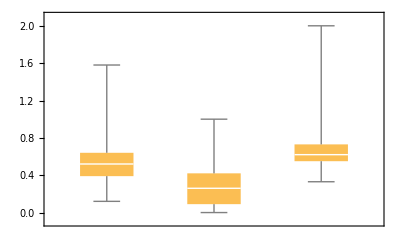

```mathematica
BoxWhiskerChart[{data[[All,2]],data[[All,3]],data[[All,10]]}] (*Рассмотрим ящики с усами для трех переменных, лежащих примерно в одних диапазонах*)
```

```mathematica
Table[Total[Table[MissingQ[i],{i,j}]],{j,Transpose[data]}]
```

{1600 False,1600 False,1600 False,1600 False,1600 False,1600 False,1600 False,1600 False,1600 False,1600 False,1600 False,1600 False}

## пропусков нет

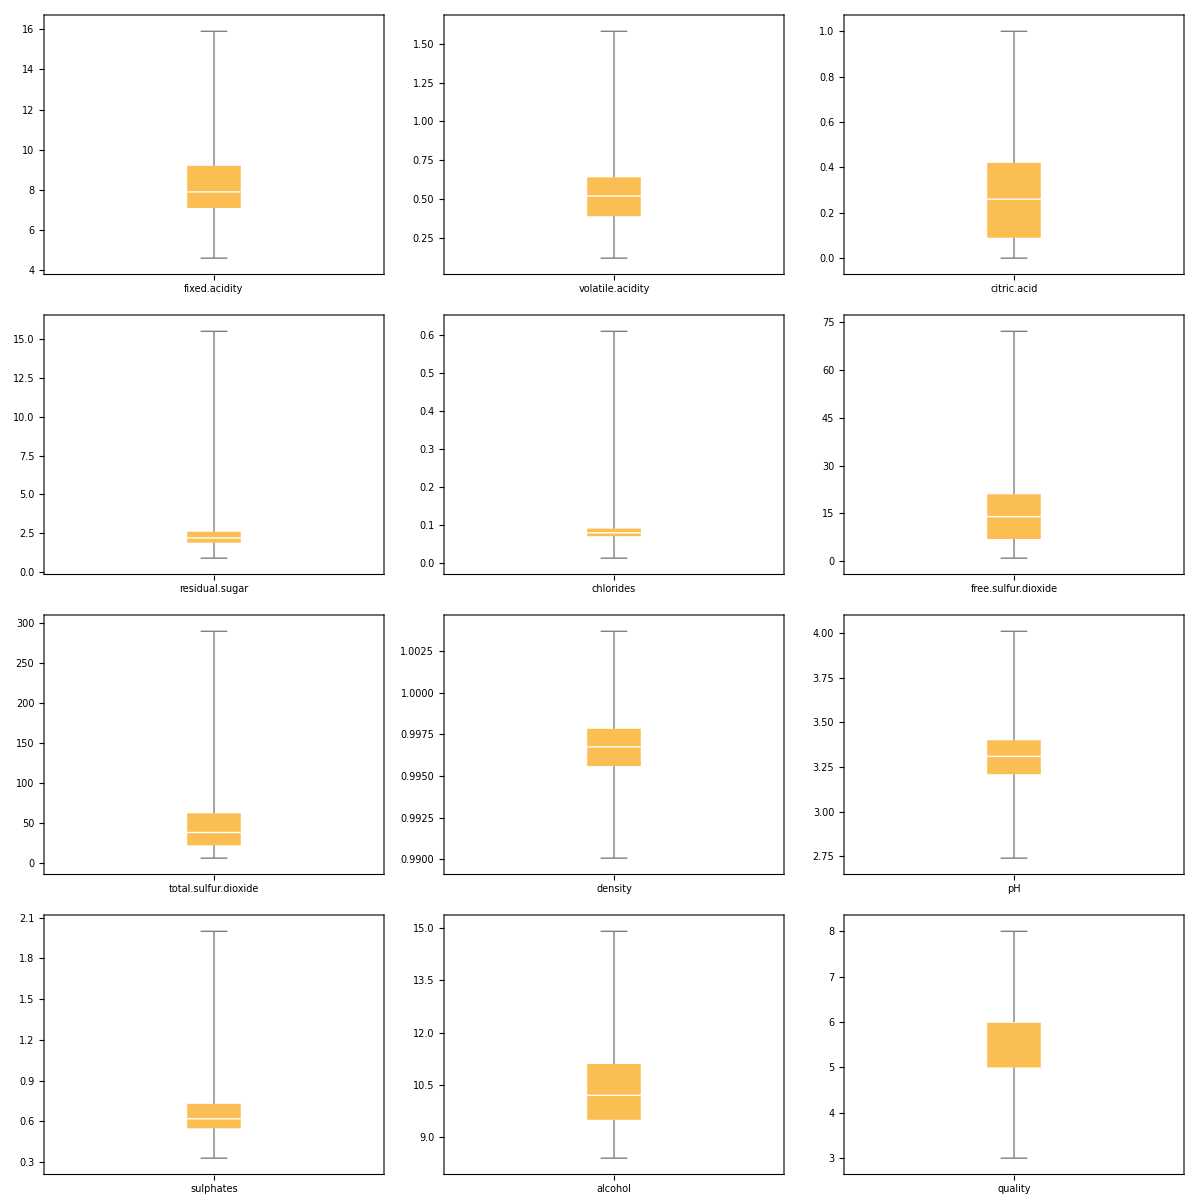

```mathematica
Grid[Partition[Table[BoxWhiskerChart[i,ChartLabels->{i[[1]]}],{i,Transpose[data]}],3]]
```

## Выбросов как таковых нет Проверка на нормальность

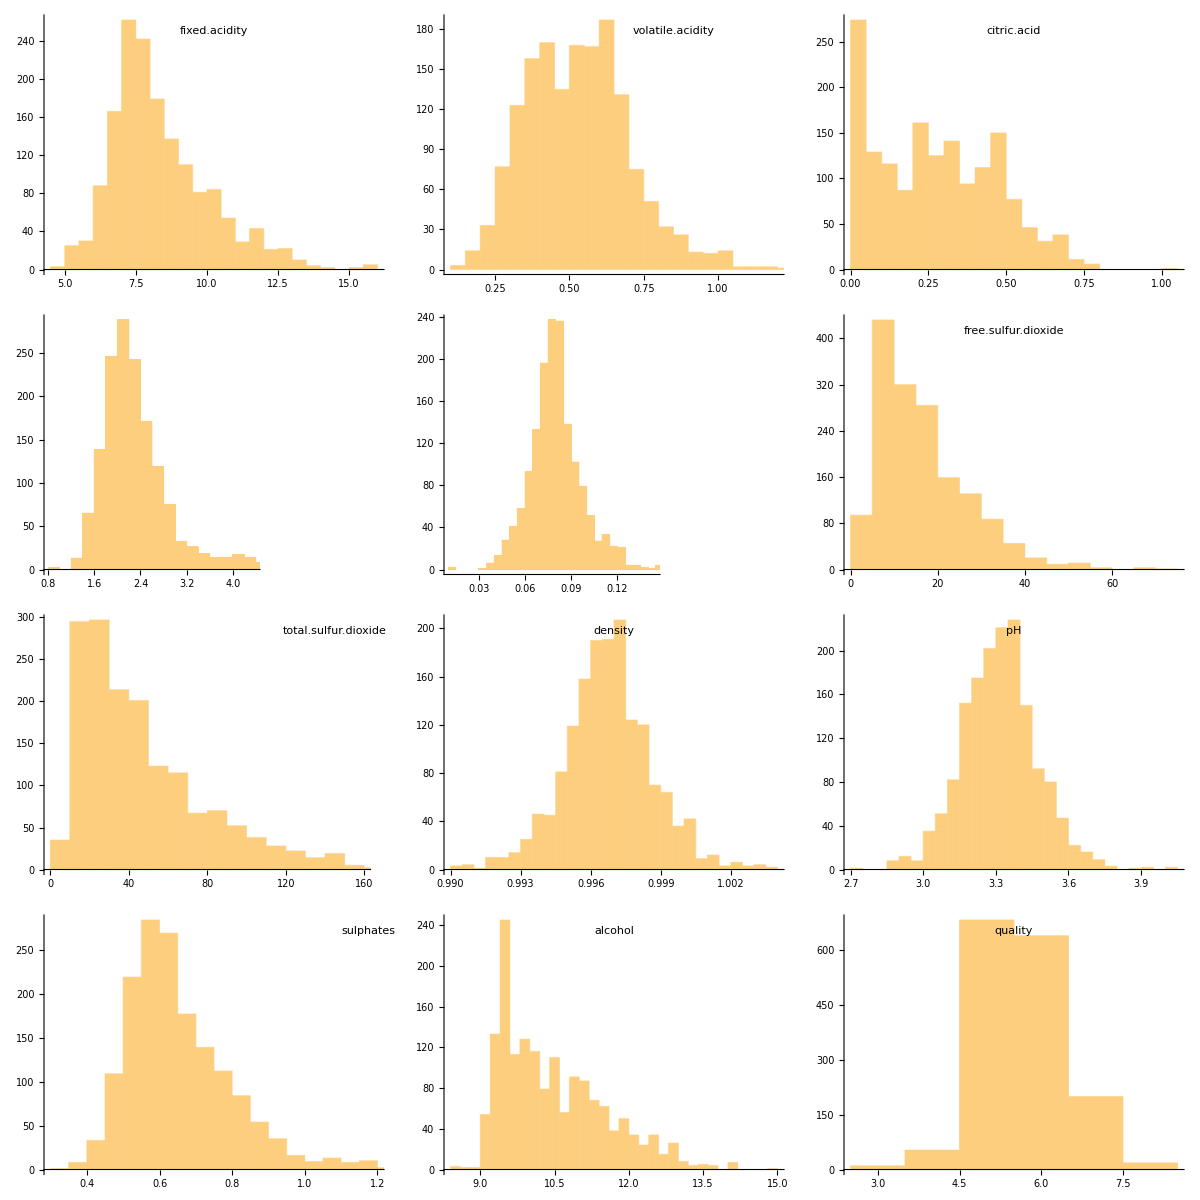

```mathematica
Grid[Partition[Table[Histogram[i,
ChartLabels->{i[[1]]}],{i,Transpose[data]}],3]]
```

```mathematica
Flatten[Transpose[data][[-1,2;;]]]
```

{5,5,5,6,5,5,5,7,7,5,5,5,5,5,5,5,7,5,4,6,6,5,5,5,6,5,5,5,5,6,5,6,5,6,5,6,6,7,4,5,5,4,6,5,5,4,5,5,5,5,5,6,6,5,6,5,5,5,5,6,5,5,7,5,5,5,5,5,5,6,6,5,5,4,5,5,5,6,5,4,5,5,5,5,6,5,6,5,5,5,5,6,5,5,4,6,5,5,5,6,6,6,6,5,5,5,5,5,6,5,5,5,5,6,5,6,6,6,6,6,5,6,5,5,5,5,5,5,7,5,5,5,5,6,6,5,5,5,5,5,5,5,6,5,6,5,5,5,6,6,6,4,5,5,5,5,5,5,5,6,5,4,6,5,5,5,5,4,6,5,4,6,6,6,5,5,5,6,5,5,5,5,5,5,6,5,5,5,5,5,5,6,5,5,5,5,5,6,7,4,7,5,5,5,6,7,7,5,5,7,6,6,6,5,6,5,5,5,5,5,6,5,5,6,4,6,6,5,6,5,7,6,6,5,6,6,6,6,6,6,5,6,6,7,7,6,5,5,6,6,6,6,5,5,6,5,5,5,5,7,5,4,5,5,5,7,4,8,6,6,6,6,5,5,5,6,6,6,8,7,6,7,5,7,5,5,6,6,7,5,7,5,6,6,6,5,5,5,5,5,6,6,5,5,5,6,5,6,6,6,6,6,6,5,5,6,5,6,7,6,7,5,5,6,6,6,7,5,6,5,6,6,6,5,7,7,6,5,6,7,6,6,6,6,6,5,7,6,6,6,6,6,5,5,6,6,5,7,7,6,5,6,5,5,7,6,7,5,5,7,5,6,6,5,6,7,6,7,6,6,6,6,6,6,5,6,6,6,6,7,8,6,5,5,5,7,5,6,6,5,5,6,6,6,5,6,6,7,6,4,6,5,5,7,5,5,6,5,6,5,7,7,5,7,5,7,6,6,5,6,7,5,6,5,6,5,6,6,6,5,8,6,7,7,7,6,5,5,6,6,6,6,6,7,5,8,5,5,7,3,6,5,5,5,6,5,6,6,6,5,5,6,6,5,6,5,5,6,5,6,5,8,5,5,6,5,5,6,7,6,6,7,7,6,6,8,6,5,8,6,6,7,7,7,7,7,7,6,6,7,5,6,6,7,7,5,6,3,6,5,6,5,5,5,5,5,5,6,6,5,6,5,5,6,6,6,5,6,7,5,5,6,5,6,6,5,6,6,6,6,6,6,6,5,5,5,6,5,6,6,5,5,5,6,6,5,6,6,6,6,6,6,5,4,6,6,4,5,5,6,5,5,5,7,7,6,7,5,8,7,5,6,5,5,5,5,6,6,6,6,4,6,5,6,6,6,7,6,6,6,5,5,6,5,6,5,5,6,5,5,5,5,5,6,5,5,5,5,6,5,6,5,6,4,5,5,5,5,7,6,5,5,5,5,5,7,5,4,7,6,5,5,5,6,5,5,5,7,6,4,6,5,6,6,5,5,6,6,5,6,5,5,5,5,6,5,6,5,5,5,5,6,5,5,5,5,5,5,5,5,3,5,5,5,5,6,6,6,5,6,6,6,6,4,4,5,5,5,6,6,5,5,5,5,5,6,5,5,5,5,5,5,5,5,4,5,6,5,5,6,5,5,5,5,5,5,5,6,5,5,6,5,5,5,5,6,6,5,6,6,5,5,5,5,6,6,6,5,5,5,5,5,6,5,6,6,5,5,6,5,6,5,5,6,6,5,6,6,5,5,6,5,5,5,5,5,5,6,6,5,6,5,6,5,6,5,5,7,6,6,5,5,7,6,6,7,7,7,5,6,5,6,5,4,6,5,6,6,5,5,5,7,5,5,5,5,7,5,8,6,4,6,3,4,5,5,7,7,7,5,7,5,6,5,6,5,5,6,5,5,5,5,5,6,6,7,6,7,7,6,5,6,5,5,5,5,6,6,6,6,6,5,4,7,7,7,4,6,6,5,5,6,6,5,6,5,6,7,6,5,5,5,6,5,6,6,7,6,7,3,5,7,7,7,7,5,5,6,6,6,6,6,6,7,6,6,5,6,6,6,5,6,6,6,5,7,6,4,5,7,5,5,6,5,5,6,6,4,7,5,7,7,7,7,7,7,7,7,7,7,7,7,7,7,6,5,6,6,7,5,6,5,5,6,6,6,7,5,6,5,6,6,7,5,7,5,5,5,7,5,6,5,6,6,5,6,7,5,5,6,5,5,6,5,5,6,7,7,6,6,7,7,7,7,5,7,7,7,7,5,7,6,5,6,6,6,7,6,6,5,6,6,5,6,7,6,6,5,6,7,7,7,5,6,6,7,7,5,7,6,5,6,6,7,6,6,6,5,6,6,5,5,5,7,6,6,7,5,7,7,6,8,6,6,6,6,7,7,7,5,7,5,6,6,5,7,6,5,5,7,6,7,6,6,6,5,7,6,7,7,8,6,6,7,6,5,6,5,7,5,6,6,6,6,6,5,6,7,5,6,6,7,6,6,6,6,6,6,6,5,8,6,6,6,4,7,6,6,5,6,6,5,7,7,7,6,6,6,5,6,6,6,6,6,5,6,6,7,6,6,7,6,5,6,6,5,7,7,6,5,7,6,7,5,5,5,5,7,6,6,6,6,6,6,6,6,4,7,5,6,6,5,6,5,5,6,5,6,5,4,6,5,7,5,6,6,6,6,6,6,6,7,8,5,7,7,7,5,7,7,6,5,6,6,6,6,6,6,6,6,6,6,6,6,6,5,5,5,7,5,6,5,5,4,6,4,6,6,4,4,5,5,6,5,6,5,5,5,6,6,6,5,5,5,5,5,5,6,6,6,5,4,5,4,6,6,6,6,6,8,6,6,5,5,6,6,4,6,6,7,6,6,6,6,5,5,6,5,5,5,5,6,6,4,6,5,5,6,6,3,6,6,6,5,5,5,5,4,5,5,5,6,5,6,6,6,6,6,6,6,5,6,5,7,6,6,6,6,5,6,6,5,6,5,5,6,5,5,5,6,6,6,6,6,5,6,5,5,5,5,5,6,5,5,5,5,5,6,5,6,5,5,6,4,6,5,5,6,6,4,5,6,5,5,3,5,5,6,6,6,6,5,5,5,5,5,5,5,5,5,6,5,5,5,5,6,5,5,7,6,5,5,6,8,6,7,6,6,7,6,6,6,6,5,5,5,5,7,5,5,5,5,6,4,6,6,6,5,5,5,5,6,6,7,6,6,5,5,5,6,7,6,5,5,6,6,5,5,5,8,7,7,7,5,6,6,6,5,5,7,6,4,6,6,5,5,7,4,7,3,5,5,6,5,5,7,5,7,3,5,4,5,4,5,4,5,5,5,5,6,6,5,5,5,7,6,5,6,6,6,5,5,5,6,6,3,6,6,6,5,6,5,6,6,6,6,5,6,5,5,6,4,5,5,6,5,6,6,6,6,6,5,6,5,7,6,6,6,5,5,6,7,6,6,7,6,5,5,5,8,5,5,6,5,6,7,5,6,5,5,5,5,5,5,5,6,6,5,5,6,6,6,5,6,6,6,6,6,6,5,6,5,5,5,7,6,6,6,6,5,6,6,6,6,5,6,6,5,6}

```mathematica
h1=DistributionFitTest[Flatten[Transpose[data][[-1,2;;]]],Automatic,"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
h1["TestDataTable",All]//N
```

| Statistic | P-Value
Anderson-Darling | 110.671 | 0.
Baringhaus-Henze | 195.154 | 0.
Cramér-von Mises | 20.1583 | 0.
Jarque-Bera ALM | 18.5495 | 0.000798425
Mardia Combined | 18.5495 | 0.000798425
Mardia Kurtosis | 2.38368 | 0.0171405
Mardia Skewness | 12.6184 | 0.000381971
Pearson χ^2 | 20710.7 | 0.
Shapiro-Wilk | 0.85759 | 9.51509×10^-36

```mathematica
Целевая переменная распределена нормально
```

Целевая нормально переменная распределена

```mathematica
2. База данных
```

2. База данных

```mathematica
names=data[[1]]   
db=Dataset[Function[AssociationThread[names->#]]/@data[[2;;]]]
```

{fixed.acidity,volatile.acidity,citric.acid,residual.sugar,chlorides,free.sulfur.dioxide,total.sulfur.dioxide,density,pH,sulphates,alcohol,quality}

Dataset[<>]

## Запросы и ответы на них

### Сколько лучшего качества представлено в выборке?

```mathematica
db[Counts,"quality"]
```

Dataset[<>]

```mathematica
Ответ: всего 18 вин лучшего качества (качества 8)
```

Ответ:144 вин всего лучшего качества^2

### Какое среднее значение содержания спирта в винах качества меньше 5?

```mathematica
d=db[Select[#quality<5&]/*Mean,"alcohol"]
```

10.2159

#### Подсчитать количество вин, у которых значение содержания спирта ниже среднего

```mathematica
d=db[Select[#alcohol<Mean[db[All,"alcohol"]]&]]  //Length
```

916

### Среднее количество уксусной кислоты в винах лучшего качества

```mathematica
d=db[Select[#quality==8&]/*Mean,"volatile.acidity"]
```

0.423333

### Сравнить среднее значение уксусной кислоты в винах худшего качества с винами лучшего

```mathematica
d=db[Select[#quality==3&]/*Mean,"volatile.acidity"]
```

0.8845

### В винах худшего качества значение уксусной кислоты в два раза больше

### Сравнить среднюю плотность вина в винах качества больше 6 и меньше 6

```mathematica
d1=db[Select[#quality≥6&]/*Mean,"density"]
```

0.996467

```mathematica
d2=db[Select[#quality<6&]/*Mean,"density"]
```

0.997068

```mathematica
Плотность практически равна
```

равна Плотность практически

#### Какое максимальное значение содержания лимонной кислоты во всех винах, качество которых больше 5?

```mathematica
d1=db[Select[#quality≥5&]/*Max,"citric.acid"]
```

0.79

### Построить распределение содержание солей в винах лучшего и худшего качества

```mathematica
d1=db[Select[#quality==8&],"chlorides"];
d2=db[Select[#quality==3&],"chlorides"];
```

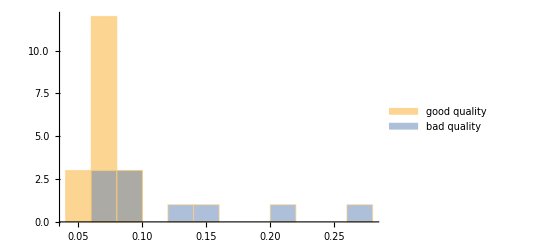

```mathematica
Histogram[{d1//Normal,d2//Normal},ChartLegends->{"good quality","bad quality"}]
```

```mathematica
У вин хорошего качества содержнание солей  меньше, у вин плохо сильно разбросано содержание солей
```

### Построить таблицу, в которой будет минимальное, максимальное и среднее значение содержания спирта по винам каждого качества

```mathematica
Table[{i,db[Select[#quality==i&]/*Min,"alcohol"] ,db[Select[#quality==i&]/*Max,"alcohol"],db[Select[#quality==i&]/*Mean,"alcohol"] }  ,{i,3,8}];
```

```mathematica
Join[{{"qual","min","max","mean"}},%];
```

```mathematica
%//TableForm
```

qual | min | max | mean
3 | 8.4 | 11 | 9.955
4 | 9 | 13.1 | 10.2651
5 | 8.5 | 14.9 | 9.89971
6 | 8.4 | 14 | 10.6295
7 | 9.2 | 14 | 11.4659
8 | 9.8 | 14 | 12.0944

### Сравнить медианы содержания сахара в винах двух категорий - качество больше 5 и качество меньше 5.

```mathematica
d1=db[Select[#quality≥6&]/*Median,"residual.sugar"]
d2=db[Select[#quality<6&]/*Median,"residual.sugar"]
```

2.2

2.2

```mathematica
Length[data[[1]]]-1
```

11

```mathematica
data⟦2;;⟧
```

{{7.4,0.7,0,1.9,0.076,11,34,0.9978,3.51,0.56,9.4,5},{7.8,0.88,0,2.6,0.098,25,67,0.9968,3.2,0.68,9.8,5},{7.8,0.76,0.04,2.3,0.092,15,54,0.997,3.26,0.65,9.8,5},{11.2,0.28,0.56,1.9,0.075,17,60,0.998,3.16,0.58,9.8,6},{7.4,0.7,0,1.9,0.076,11,34,0.9978,3.51,0.56,9.4,5},{7.4,0.66,0,1.8,0.075,13,40,0.9978,3.51,0.56,9.4,5},{7.9,0.6,0.06,1.6,0.069,15,59,0.9964,3.3,0.46,9.4,5},{7.3,0.65,0,1.2,0.065,15,21,0.9946,3.39,0.47,10,7},{7.8,0.58,0.02,2,0.073,9,18,0.9968,3.36,0.57,9.5,7},{7.5,0.5,0.36,6.1,0.071,17,102,0.9978,3.35,0.8,10.5,5},1579,{6.6,0.725,0.2,7.8,0.073,29,79,0.9977,3.29,0.54,9.2,5},{6.3,0.55,0.15,1.8,0.077,26,35,0.99314,3.32,0.82,11.6,6},{5.4,0.74,0.09,1.7,0.089,16,26,0.99402,3.67,0.56,11.6,6},{6.3,0.51,0.13,2.3,0.076,29,40,0.99574,3.42,0.75,11,6},{6.8,0.62,0.08,1.9,0.068,28,38,0.99651,3.42,0.82,9.5,6},{6.2,0.6,0.08,2,0.09,32,44,0.9949,3.45,0.58,10.5,5},{5.9,0.55,0.1,2.2,0.062,39,51,0.99512,3.52,0.76,11.2,6},{6.3,0.51,0.13,2.3,0.076,29,40,0.99574,3.42,0.75,11,6},{5.9,0.645,0.12,2,0.075,32,44,0.99547,3.57,0.71,10.2,5},{6,0.31,0.47,3.6,0.067,18,42,0.99549,3.39,0.66,11,6}}
 |  |  |  |

```mathematica
lm = LinearModelFit[data⟦2;;⟧,{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11},{x1,x2,x3,x4,x5,x6,x7,x8,x9,x10,x11}]
```

FittedModel[21.9652+0.0249906 x1+0.916334 x10+0.276198 x11-1.08359 x2-0.182564 x3+0.0163313 x4-1.87423 x5+0.00436133 x6-0.00326458 x7-17.8812 x8-0.413653 x9]

```mathematica
lm["AdjustedRSquared"]
```

0.356119

```mathematica
Факторный Анализ
```

Анализ Факторный

## Кластерный анализ

```mathematica
FindClusters[Flatten[Transpose[data]⟦-1,2;;⟧],5]
```

{{5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,4,5,5,4,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,4,5,5,5,5,4,5,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,4,5,4,5,5,4,5,5,5,5,5,5,4,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,4,5,5,5,5,5,5,4,5,4,5,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5},{6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6},{7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,7,7,7,7,7,7,7,7,8,7,7,7,7,8,7,8,7,7,7,8,8,7,7,7,7,7,7,7,7,7,7,7,7,7,8,7,7,7,7,7,7,7,7,7,7,7,7,7,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,7,7,7,7,7,7,7,7,7,7,8,7,7,7,7,8,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,7,7,7,7,7,7,8,7,7,7,8,7,7,7,7,7,8,7,7,7,7,7,7,7,7,7,7,7,7,8,7,7},{3,3,3,3,3,3,3,3,3,3}}

```mathematica
Needs["HierarchicalClustering`"]
```

Agglomerate::ties: 21 ties have been detected; reordering input may produce a different result.

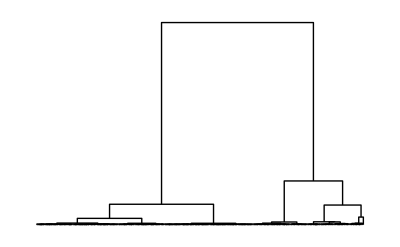

Agglomerate::ties: 21 ties have been detected; reordering input may produce a different result.

-Graphics-

Agglomerate::ties: 21 ties have been detected; reordering input may produce a different result.

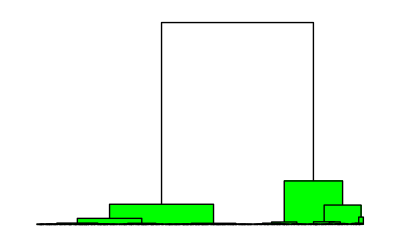

```mathematica
DendrogramPlot[data⟦2;;⟧,Linkage->"Ward"]
DendrogramPlot[Agglomerate[data⟦2;;⟧,Linkage->"Ward"]]
DendrogramPlot[data⟦2;;⟧,Linkage->"Ward",HighlightLevel->2]
```

```mathematica
d = data⟦2;;⟧;
```

```mathematica
dc=Correlation[d]
```

{{1.,-0.256131,0.671703,0.114777,0.0937052,-0.153794,-0.113181,0.668047,-0.682978,0.183006,-0.0616683,0.124052},{-0.256131,1.,-0.552496,0.00191788,0.0612978,-0.0105038,0.07647,0.0220262,0.234937,-0.260987,-0.202288,-0.390558},{0.671703,-0.552496,1.,0.143577,0.203823,-0.0609781,0.035533,0.364947,-0.541904,0.31277,0.109903,0.226373},{0.114777,0.00191788,0.143577,1.,0.0556095,0.187049,0.203028,0.355283,-0.0856524,0.00552712,0.0420754,0.0137316},{0.0937052,0.0612978,0.203823,0.0556095,1.,0.00556215,0.0474005,0.200632,-0.265026,0.37126,-0.221141,-0.128907},{-0.153794,-0.0105038,-0.0609781,0.187049,0.00556215,1.,0.667666,-0.0219458,0.0703775,0.0516576,-0.0694084,-0.0506561},{-0.113181,0.07647,0.035533,0.203028,0.0474005,0.667666,1.,0.0712695,-0.0664946,0.0429468,-0.205654,-0.1851},{0.668047,0.0220262,0.364947,0.355283,0.200632,-0.0219458,0.0712695,1.,-0.341699,0.148506,-0.49618,-0.174919},{-0.682978,0.234937,-0.541904,-0.0856524,-0.265026,0.0703775,-0.0664946,-0.341699,1.,-0.196648,0.205633,-0.0577314},{0.183006,-0.260987,0.31277,0.00552712,0.37126,0.0516576,0.0429468,0.148506,-0.196648,1.,0.0935948,0.251397},{-0.0616683,-0.202288,0.109903,0.0420754,-0.221141,-0.0694084,-0.205654,-0.49618,0.205633,0.0935948,1.,0.476166},{0.124052,-0.390558,0.226373,0.0137316,-0.128907,-0.0506561,-0.1851,-0.174919,-0.0577314,0.251397,0.476166,1.}}

```mathematica
T=PrincipalComponents[dc,Method->"Correlation"]//MatrixForm
```

(2.80351 | 0.0618043 | 0.682129 | 0.845118 | 1.03359 | 0.107609 | 0.0802278 | 0.133726 | 0.207676 | 0.0997642 | 0.143442 | 0.
-2.84011 | 1.31037 | 2.15811 | 0.144812 | 0.370599 | 0.261538 | 0.663487 | 0.304893 | -0.0239153 | -0.15844 | -0.0189237 | 0.
2.79838 | -0.581437 | -0.346887 | 0.180423 | 0.501978 | 0.425901 | -0.573477 | 0.0837548 | -0.212519 | -0.283119 | -0.0435536 | 0.
0.115335 | 1.09571 | -0.697056 | 1.99268 | -1.83552 | 0.000482377 | 0.0572681 | 0.0506594 | -0.0333282 | -0.0510181 | 0.0448125 | 0.
1.00689 | 1.06073 | 1.22187 | -1.92475 | -0.88125 | 0.806441 | -0.185144 | -0.467999 | 0.048482 | 0.0894936 | 0.00936833 | 0.
-1.61494 | 1.34142 | -2.17482 | -0.486558 | 0.42569 | 0.00298574 | 0.0354699 | -0.218643 | 0.615164 | -0.0839091 | -0.0130961 | 0.
-1.27309 | 2.00198 | -1.8655 | -0.450107 | 0.565977 | 0.200572 | 0.0764058 | 0.196553 | -0.569121 | 0.141125 | 0.0132528 | 0.
1.83312 | 1.93338 | 0.937398 | 0.929136 | 0.293987 | -0.684139 | -0.122584 | -0.186363 | 0.0556439 | 0.143725 | -0.130841 | 0.
-3.79344 | -1.13652 | 0.898638 | 0.106664 | 0.148454 | -0.578176 | -0.829196 | -0.254657 | -0.0832597 | -0.00117066 | 0.0552896 | 0.
1.56573 | -0.788676 | -0.11589 | -1.93939 | -0.599998 | -0.977256 | 0.18257 | 0.571167 | 0.0101052 | -0.0431799 | 0.0179328 | 0.
-1.02177 | -3.27519 | -0.219148 | 0.435873 | -0.159978 | 0.619992 | -0.0925361 | 0.561619 | 0.179515 | 0.16604 | -0.0702275 | 0.
0.420387 | -3.02356 | -0.478837 | 0.166094 | 0.136467 | -0.185951 | 0.707508 | -0.774711 | -0.194443 | -0.0193109 | -0.00745566 | 0.)

```mathematica
{u,w,v}=SingularValueDecomposition[dc]; (* отличается знаком от PCA - PrincipalComponents *)
T1=u.w;  (*  см. Т для РСА, новые переменные (факторы) *)
T1//MatrixForm
P1=v;   (*  факторы  = РР  *)
P1//MatrixForm
w;
%//MatrixForm
```

(-1.52277 | -0.00935585 | 0.277393 | -0.280789 | 0.0766731 | 0.0367946 | -0.189956 | -0.101442 | 0.0718053 | -0.0599948 | -0.0462149 | 0.0380069
0.827512 | 0.759926 | 0.382172 | 0.0508586 | -0.291375 | 0.19698 | -0.387211 | -0.0739212 | 0.0247703 | 0.0508621 | 0.0679715 | 0.000277454
-1.47736 | -0.307941 | -0.168677 | -0.0689352 | 0.116936 | 0.0905322 | 0.150961 | -0.149907 | 0.0908887 | 0.113488 | 0.112516 | -0.00416845
-0.434324 | 0.376045 | -0.409993 | -0.465399 | -0.690397 | 0.0724284 | 0.175512 | 0.0863151 | -0.114421 | -0.0171294 | 0.0158733 | 0.0109302
-0.616202 | 0.425483 | 0.0447789 | 0.795569 | -0.259119 | 0.223517 | 0.142551 | 0.094559 | 0.172723 | -0.00126667 | -0.0375966 | 0.00320987
0.143201 | 0.581731 | -1.03687 | -0.0409602 | 0.155151 | -0.0282583 | -0.0854889 | 0.00979171 | 0.130796 | -0.19196 | 0.04288 | -0.00309027
-0.012693 | 0.815981 | -0.910009 | -0.0345792 | 0.212612 | 0.07683 | -0.068144 | -0.0454762 | -0.0501066 | 0.193206 | -0.0639861 | 0.00415393
-1.15577 | 0.741572 | 0.283947 | -0.243847 | -0.203211 | -0.282044 | -0.0757727 | -0.040217 | 0.102446 | 0.014277 | -0.0417122 | -0.0337255
1.35059 | -0.146709 | -0.117418 | -0.00664152 | -0.250758 | -0.318279 | 0.114816 | -0.159195 | 0.18999 | 0.0680793 | -0.00100906 | 0.0203093
-0.794448 | -0.245113 | -0.358316 | 0.681022 | -0.209091 | -0.267517 | -0.144317 | -0.139364 | -0.186194 | -0.0235835 | 0.017596 | 0.0040349
0.228397 | -1.12701 | -0.378609 | -0.111419 | -0.252782 | 0.259853 | -0.0752609 | -0.238361 | 0.0397027 | -0.0362696 | -0.0576607 | -0.0189053
-0.351096 | -1.06078 | -0.375913 | -0.0445539 | -0.133906 | -0.0939758 | -0.254987 | 0.309719 | 0.0988138 | 0.0853377 | 0.0094553 | 0.000504145)

(-0.487883 | -0.00417321 | 0.164829 | -0.231098 | 0.0787794 | 0.0555313 | -0.307215 | -0.200529 | 0.174578 | -0.182956 | -0.256438 | 0.63858
0.265129 | 0.338968 | 0.227089 | 0.0418582 | -0.299379 | 0.297287 | -0.626234 | -0.146126 | 0.0602233 | 0.155106 | 0.377161 | 0.00466168
-0.473335 | -0.137358 | -0.100229 | -0.0567358 | 0.120149 | 0.136633 | 0.244149 | -0.296333 | 0.220975 | 0.346086 | 0.624328 | -0.0700369
-0.139154 | 0.167736 | -0.24362 | -0.383038 | -0.709363 | 0.109311 | 0.283854 | 0.170626 | -0.278187 | -0.0522366 | 0.0880779 | 0.183646
-0.197427 | 0.189788 | 0.0266079 | 0.654778 | -0.266237 | 0.337337 | 0.230547 | 0.186923 | 0.419936 | -0.00386273 | -0.208617 | 0.0539312
0.0458807 | 0.259483 | -0.616111 | -0.0337115 | 0.159413 | -0.0426481 | -0.13826 | 0.0193561 | 0.318 | -0.585389 | 0.237933 | -0.0519217
-0.00406675 | 0.363971 | -0.540732 | -0.0284597 | 0.218453 | 0.115954 | -0.110209 | -0.0898966 | -0.121823 | 0.589188 | -0.355047 | 0.069793
-0.370301 | 0.330781 | 0.168723 | -0.200693 | -0.208793 | -0.425667 | -0.122546 | -0.0795002 | 0.249074 | 0.0435381 | -0.231453 | -0.566645
0.432721 | -0.0654401 | -0.0697706 | -0.00546618 | -0.257647 | -0.480354 | 0.185692 | -0.314693 | 0.461916 | 0.20761 | -0.00559907 | 0.34123
-0.254535 | -0.109334 | -0.212913 | 0.560502 | -0.214835 | -0.403743 | -0.233402 | -0.275492 | -0.452689 | -0.0719186 | 0.097637 | 0.067793
0.0731768 | -0.502709 | -0.224971 | -0.0917014 | -0.259726 | 0.392176 | -0.121719 | -0.471189 | 0.096528 | -0.110605 | -0.319949 | -0.31764
-0.112489 | -0.473166 | -0.223369 | -0.0366692 | -0.137584 | -0.14183 | -0.412388 | 0.612247 | 0.240243 | 0.26024 | 0.0524657 | 0.00847048)

(3.12117 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 2.24188 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1.68292 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1.21502 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.973264 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.662592 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.618318 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.505873 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.411308 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.327919 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.180219 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0595179)

```mathematica
tt=Transpose[T1].T1//Chop
```

{{9.74169,0,0,0,0,0,0,0,0,0,0,0},{0,5.02604,0,0,0,0,0,0,0,0,0,0},{0,0,2.83222,0,0,0,0,0,0,0,0,0},{0,0,0,1.47628,0,0,0,0,0,0,0,0},{0,0,0,0,0.947242,0,0,0,0,0,0,0},{0,0,0,0,0,0.439028,0,0,0,0,0,0},{0,0,0,0,0,0,0.382317,0,0,0,0,0},{0,0,0,0,0,0,0,0.255907,0,0,0,0},{0,0,0,0,0,0,0,0,0.169174,0,0,0},{0,0,0,0,0,0,0,0,0,0.107531,0,0},{0,0,0,0,0,0,0,0,0,0,0.0324788,0},{0,0,0,0,0,0,0,0,0,0,0,0.00354238}}

```mathematica
(*Собственные числа*)
```

```mathematica
dval=Eigenvalues[dc]
dvec=Eigenvectors[dc];
%//MatrixForm
```

{3.12117,2.24188,1.68292,1.21502,0.973264,0.662592,0.618318,0.505873,0.411308,0.327919,0.180219,0.0595179}

(0.487883 | -0.265129 | 0.473335 | 0.139154 | 0.197427 | -0.0458807 | 0.00406675 | 0.370301 | -0.432721 | 0.254535 | -0.0731768 | 0.112489
-0.00417321 | 0.338968 | -0.137358 | 0.167736 | 0.189788 | 0.259483 | 0.363971 | 0.330781 | -0.0654401 | -0.109334 | -0.502709 | -0.473166
0.164829 | 0.227089 | -0.100229 | -0.24362 | 0.0266079 | -0.616111 | -0.540732 | 0.168723 | -0.0697706 | -0.212913 | -0.224971 | -0.223369
0.231098 | -0.0418582 | 0.0567358 | 0.383038 | -0.654778 | 0.0337115 | 0.0284597 | 0.200693 | 0.00546618 | -0.560502 | 0.0917014 | 0.0366692
-0.0787794 | 0.299379 | -0.120149 | 0.709363 | 0.266237 | -0.159413 | -0.218453 | 0.208793 | 0.257647 | 0.214835 | 0.259726 | 0.137584
-0.0555313 | -0.297287 | -0.136633 | -0.109311 | -0.337337 | 0.0426481 | -0.115954 | 0.425667 | 0.480354 | 0.403743 | -0.392176 | 0.14183
0.307215 | 0.626234 | -0.244149 | -0.283854 | -0.230547 | 0.13826 | 0.110209 | 0.122546 | -0.185692 | 0.233402 | 0.121719 | 0.412388
-0.200529 | -0.146126 | -0.296333 | 0.170626 | 0.186923 | 0.0193561 | -0.0898966 | -0.0795002 | -0.314693 | -0.275492 | -0.471189 | 0.612247
0.174578 | 0.0602233 | 0.220975 | -0.278187 | 0.419936 | 0.318 | -0.121823 | 0.249074 | 0.461916 | -0.452689 | 0.096528 | 0.240243
0.182956 | -0.155106 | -0.346086 | 0.0522366 | 0.00386273 | 0.585389 | -0.589188 | -0.0435381 | -0.20761 | 0.0719186 | 0.110605 | -0.26024
0.256438 | -0.377161 | -0.624328 | -0.0880779 | 0.208617 | -0.237933 | 0.355047 | 0.231453 | 0.00559907 | -0.097637 | 0.319949 | -0.0524657
0.63858 | 0.00466168 | -0.0700369 | 0.183646 | 0.0539312 | -0.0519217 | 0.069793 | -0.566645 | 0.34123 | 0.067793 | -0.31764 | 0.00847048)

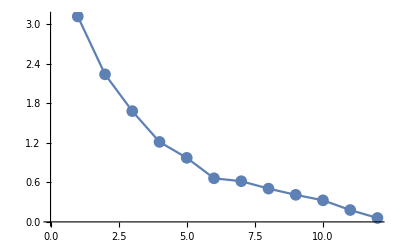

```mathematica
ListLinePlot[dval,PlotMarkers->{Automatic, Dimensions[dval][[1]]}]
```

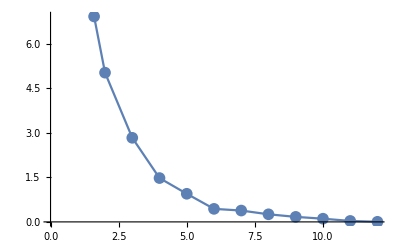

```mathematica
ListLinePlot[Diagonal[tt],PlotMarkers->{Automatic, Dimensions[dval][[1]]}]
```